## Initialization

```mathematica
(* Switch to the directory the notebook and data files are in *)
SetDirectory[NotebookDirectory[]]
```

/Users/npadmana/myWork/np_sandbox/diff_transfer_fn

/Users/npadmana/myWork/np_sandbox/diff_transfer_fn

/Users/npadmana/myWork/np_sandbox/diff_transfer_fn

«1 more identical outputs»

```mathematica
(* Number of files *)
```

```mathematica
nfiles = 5;
```

```mathematica
(* zvals -- hardcoded is not ideal, but why not?? *)
```

```mathematica
zvals= {0.04, 0.03, 0.02, 0.01, 0.00};
```

```mathematica
(* Set the file name list *)
```

```mathematica
fnames = "test_transfer_z"<>ToString[#]<>".dat"& /@ Range[0,nfiles-1];
```

```mathematica
(* Read in all the files *)
```

```mathematica
tData = Import[#, "Table"] & /@ fnames;
```

```mathematica
Dimensions[tData]
```

{5,692,7}

{5,692,7}

{5,692,7}

```mathematica
kval = tData[[1,All,1]];
```

```mathematica
transfers = tData[[All, All, {2,3}]];
```

```mathematica
Dimensions[transfers]
```

{5,692,2}

{5,692,2}

{5,692,2}

### Normalization

The CAMB transfer functions are normalized to make it easy to compute power spectra, but this is inconvenient when computing derivatives of transfer functions. So let us remove and store the normalizations. I

```mathematica
norms = transfers[[All, 1, All]]
```

{{1.99711×10^7,1.99711×10^7},{2.00696×10^7,2.00696×10^7},{2.01684×10^7,2.01684×10^7},{2.02675×10^7,2.02675×10^7},{2.03668×10^7,2.03668×10^7}}

```mathematica
transfer1 = Transpose[ Transpose[transfers, {1,3,2}]/norms, {1,3,2}];
```

```mathematica
tNorm1 = transfer1[[All,All,2]]- transfer1[[All,All,1]];
```

```mathematica
tDiffDot=-D[Fit[Thread[{zvals, tNorm1[[All,#]]}], {1, z}, z],z]/.z->0 & /@ Range[Dimensions[tNorm1][[2]]];
```

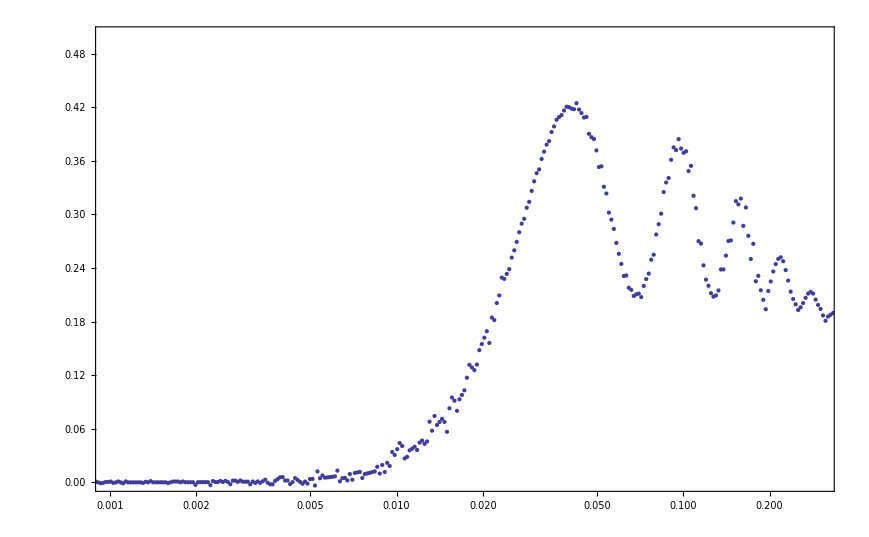

```mathematica
ListLogLinearPlot[Thread[{kval, tDiffDot*kval*1*^4}], Frame->True, PlotRange->{{0.001, 0.3}, {0, 0.5}}]
```

```mathematica
normCDM = norms[[All, 2]]/norms[[5,2]]
```

{0.980571,0.985408,0.990259,0.995124,1.}

```mathematica
dDot =-D[Fit[Thread[{zvals,normCDM}], {1,z},z], z] /. z->0
```

0.485742

```mathematica
tVRel = (tDiffDot -dDot * tNorm1[[5,All]] )*kval;
```

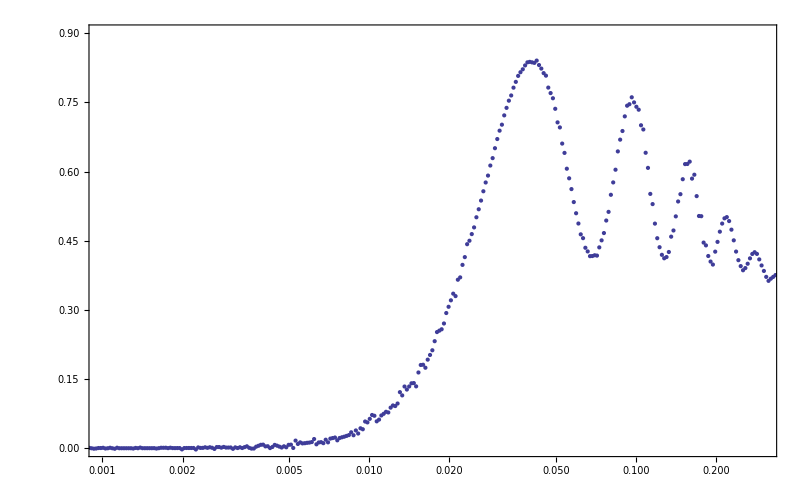

```mathematica
ListLogLinearPlot[Thread[{kval, tVRel*1*^4}], Frame->True,  PlotRange->{{0.001,0.3}, {0,0.9}}]
```

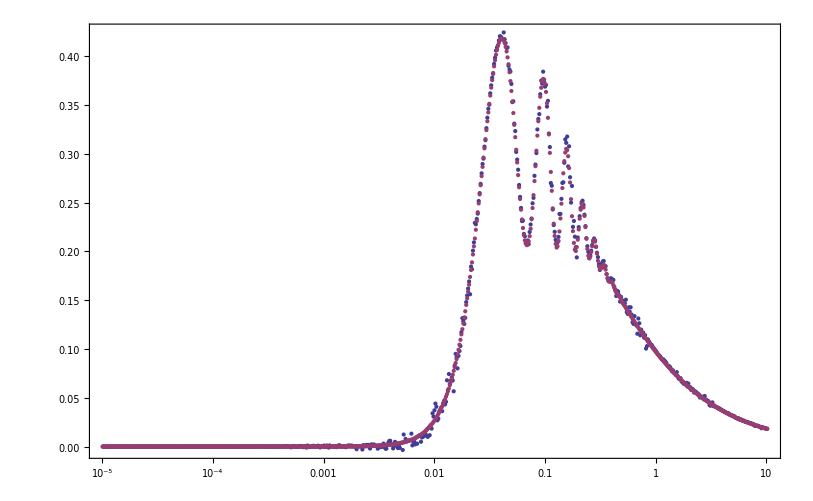

```mathematica
ListLogLinearPlot[{Thread[{kval, kval*tDiffDot*1*^4}], Thread[{kval, -kval*dDot * tNorm1[[5,All]] * 1*^4}]}, Frame->True,  PlotRange->Full]
```